### Run

```mathematica
ClearAll["Global`*"]
Needs["BenderWu`"]
m=4ζ η/(1+(ζ+η)^2);
V[x_]:=JacobiSN[x,m]^2(1+(ζ-η)^2JacobiSN[x,m]^2)/JacobiDN[x,m]^2
```

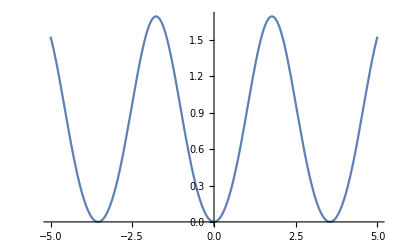

```mathematica
Plot[Evaluate[V[x]] /.{ζ-> 1/3, η-> 1/2}, {x, -5, 5}]
```

```mathematica
(*Some machinery*)
MyBW[ζin_, ηin_, nu_, order_, numeric_:0]:=BenderWu[Simplify[Evaluate[V[x]] /. ζ-> ζin /. η -> ηin], x, nu, order]
MyBWSeries[BW_]:=Collect[Sqrt[2]BWProcess[BW,OutputStyle->"Series", Coupling->2^(1/4)g],g]
```

```mathematica
(*A basic agreement in single deformation with eqn 4.7 *)
BW=MyBW[0, 1/2, 0, 4];
MyBWSeries[BW]
```

1-g^2/16-(61 g^4)/256+(777 g^6)/4096-(134933 g^8)/262144

```mathematica
(*Level Dependence for single defos*)
MyBWPolynomials=BWLevelPolynomial[Table[CoefficientList[MyBWSeries[MyBW[0,η, nu, 4]], g^2],{nu,0,6}]] //Simplify
```

{1+2 ν,1/4 (-1+3 η^2) (1+2 ν+2 ν^2),1/16 (-1-3 ν-3 ν^2-2 ν^3-2 η^2 (3+7 ν+3 ν^2+2 ν^3)-η^4 (21+59 ν+51 ν^2+34 ν^3)),1/64 (3 (-1+η^2+49 η^4+111 η^6)+(-11+11 η^2+359 η^4+1041 η^6) ν+8 (-2+2 η^2+53 η^4+177 η^6) ν^2+10 (-1+η^2+13 η^4+75 η^6) ν^3+5 (-1+η^2+13 η^4+75 η^6) ν^4),1/1024(-53-225 ν-390 ν^2-370 ν^3-165 ν^4-66 ν^5+60 η^2 (1+5 ν+10 ν^2+10 ν^3+5 ν^4+2 ν^5)-2 η^4 (615+1643 ν+1290 ν^2+1030 ν^3+255 ν^4+102 ν^5)-4 η^6 (4665+14477 ν+16050 ν^2+12730 ν^3+3045 ν^4+1218 ν^5)-η^8 (30885+111697 ν+160470 ν^2+142610 ν^3+53445 ν^4+21378 ν^5))}

```mathematica
Collect[Simplify[MyBWSeries[MyBW[ζ,η, 0, 3]]], g]
```

1+(g^2 (3 ζ^6+6 ζ^5 η+ζ^4 (5-3 η^2)+(1+η^2)^2 (-1+3 η^2)+ζ^3 (4 η-12 η^3)+ζ^2 (1-2 η^2-3 η^4)+ζ (-2 η+4 η^3+6 η^5)))/(4 (1+ζ^2+2 ζ η+η^2)^2)-(g^4 (21 ζ^8+ζ^6 (48-84 η^2)+(1+η^2)^2 (1+6 η^2+21 η^4)+2 ζ^4 (17-24 η^2+63 η^4)-4 ζ^2 (-2+13 η^2+12 η^4+21 η^6)))/(16 (1+ζ^2+2 ζ η+η^2)^2)+1/(64 (1+ζ^2+2 ζ η+η^2)^2)3 g^6 (111 ζ^10-222 ζ^9 η+ζ^8 (271-333 η^2)+8 ζ^7 η (-40+111 η^2)+6 ζ^6 (35-74 η^2+37 η^4)+8 ζ^3 η^3 (21+40 η^2+111 η^4)-4 ζ^5 η (25-80 η^2+333 η^4)+(1+η^2)^2 (-1+η^2+49 η^4+111 η^6)+2 ζ^4 (25-97 η^2+173 η^4+111 η^6)-2 ζ η (-1+50 η^4+160 η^6+111 η^8)-ζ^2 (1+84 η^2+194 η^4+444 η^6+333 η^8))

```mathematica
(*To find agreement with Cherman, Dorigoni and Unsal 2015 eqn 5.22*)
nodeformation[n_]:=Collect[1/2MyBWSeries[MyBW[0,0,0,n]] /. g-> 2g,g] 
nodeformation[8]
```

1/2-g^2/2-g^4/2-(3 g^6)/2-(53 g^8)/8-(297 g^10)/8-(3961 g^12)/16-(30363 g^14)/16-(2095501 g^16)/128

```mathematica
(*asymptotic form*)
a[n_]:=-2 /Pi n!(1-5/(2n) - 13/(8n^2))
asymptotic[k_]:=Sum[a[n]g^(2n), {n, 1, k}] 
asymptotic[8] //N
nodeformation [8]//N
```

1.98944 g^2+0.835563 g^4+0.0530516 g^6-4.17782 g^8-33.2316 g^10-246.69 g^12-1956.24 g^14-16995.4 g^16

0.5-0.5 g^2-0.5 g^4-1.5 g^6-6.625 g^8-37.125 g^10-247.563 g^12-1897.69 g^14-16371.1 g^16

```mathematica
(*
Timing[BW=MyBW[0.2, 0.4, 0, 8, Evaluation -> "Numerical"]; Print[Series[MyBWSeries[BW], {g, 0, 6}] ]][[1]]
Timing[BW=MyBW[0.2, 0.4, 0, 8] ; Print[Series[MyBWSeries[BW], {g, 0, 6}]]][[1]]
Timing[BW=MyBW[1/5, 2/5, 0, 8]; Print[Series[MyBWSeries[BW], {g, 0, 6}] ]][[1]]
*)
```

### Double Deformations

```mathematica
m2[ζ_, η_]:=4ζ η/(1+(ζ+η)^2);
V2[x_, ζ_, η_]:=Series[JacobiSN[x,m2[ζ,η]]^2(1+(ζ-η)^2JacobiSN[x,m2[ζ,η]]^2)/JacobiDN[x,m2[ζ,η]]^2, {x, 0, 120}] //Normal 
My2[ζ_, η_, nu_, order_, numeric_:0]:=BenderWu[V2[x, ζ, η], x, nu, order]
ζin=0.4`40;
ηin=0.4`40;
BW=My2[ζin, ηin, 0, 60];
```

1-0.054878048780487804878048780487804878049 h-0.092244199881023200475907198096371207615 h^2-0.0102896341463414634146341463414634146 h^3-0.020596958839693979781021820316721761 h^4-0.011019866864099838946039668606085228 h^5-0.020269446939573351081565243485779747 h^6-0.02001184158509502004207569347108145 h^7-0.03862650739453598069021299938296476 h^8-0.0552266587934798271252578852671742 h^9-0.117056873794220949449551069058151 h^10-0.21711098544557960862985031681614 h^11-0.51435424789154569778155822808553 h^12-1.163573370332552402971747734255 h^13-3.093069136829675786289348849049 h^14-8.21395400994736511595213572053 h^15-24.4245380581125265901317326441 h^16-74.215757734460813981378984826 h^17-245.33879023327764961989945005 h^18-837.6141258420958411161412501 h^19-3056.237221983111841513626492 h^20-11566.3890005150846145199837 h^21-46248.6346536453246432859663 h^22-192001.16128046129535340194 h^23-835705.80619512512061849013 h^24-3.774262713522920384880234×10^6 h^25-1.77743668267549084034661×10^7 h^26-8.6732088332236079255634×10^7 h^27-4.39540718722074446086392×10^8 h^28-2.3041227731735266175748×10^9 h^29-1.2505151720725694433385×10^10 h^30-7.008008829659889889283×10^10 h^31-4.055855979354193188861×10^11 h^32-2.41963451971329597102×10^12 h^33-1.48760279099634050096×10^13 h^34-9.4125007583520988598×10^13 h^35-6.1265106817991728048×10^14 h^36-4.097850695921419522×10^15 h^37-2.815201322294881665×10^16 h^38-1.98474495246278489×10^17 h^39-1.43518887453496553×10^18 h^40-1.0636849232069222×10^19 h^41-8.075848606660624×10^19 h^42-6.27721467685315×10^20 h^43-4.992656184965477×10^21 h^44-4.06112085381563×10^22 h^45-3.37679784713615×10^23 h^46-2.8687796678757×10^24 h^47-2.489036894068×10^25 h^48-2.204526348226×10^26 h^49-1.992376680265×10^27 h^50-1.83664009322×10^28 h^51-1.72626734909×10^29 h^52-1.6537190641×10^30 h^53-1.6141043491×10^31 h^54-1.60460511×10^32 h^55-1.624158953×10^33 h^56-1.673300384×10^34 h^57-1.75416749×10^35 h^58-1.87064223×10^36 h^59-2.0290244×10^37 h^60

{-3.4229,-1.5717,-0.93359,-0.637,-0.468,-0.36,-0.2863,-0.233,-0.1916,-0.1592,-0.1324,-0.10868,-0.000020247,0.0153926,0.0678,0.08,0.09,0.1,0.1,0.1,0.2,0.2,0.24,0.29,0.36,0.463,0.6245,0.90749,1.517,3.2337}

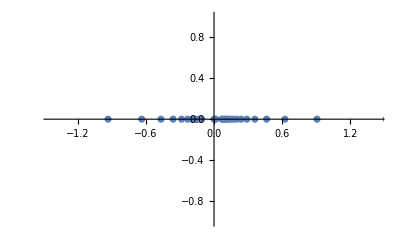

```mathematica
series=MyBWSeries[BW] /. g-> Sqrt[h]
Pade=PadeApproximant[series, {h, 0, {30, 30}}];
sol=Solve[Numerator[Pade]==0,h];
poles=Table[h/. sol[[n,1]], {n, 1, 30}]
ListPlot[Table[{ComplexExpand@Re[poles[[i]]], ComplexExpand@Im[poles[[i]]]}, {i, 1, 30}]]
```

### Critical Points

```mathematica
V'[x]
Solve[V'[x]==0, x]
```

(2 (ζ-η)^2 JacobiCN[x,(4 ζ η)/(1+(ζ+η)^2)] JacobiSN[x,(4 ζ η)/(1+(ζ+η)^2)]^3)/JacobiDN[x,(4 ζ η)/(1+(ζ+η)^2)]+(2 JacobiCN[x,(4 ζ η)/(1+(ζ+η)^2)] JacobiSN[x,(4 ζ η)/(1+(ζ+η)^2)] (1+(ζ-η)^2 JacobiSN[x,(4 ζ η)/(1+(ζ+η)^2)]^2))/JacobiDN[x,(4 ζ η)/(1+(ζ+η)^2)]+(8 ζ η JacobiCN[x,(4 ζ η)/(1+(ζ+η)^2)] JacobiSN[x,(4 ζ η)/(1+(ζ+η)^2)]^3 (1+(ζ-η)^2 JacobiSN[x,(4 ζ η)/(1+(ζ+η)^2)]^2))/((1+(ζ+η)^2) JacobiDN[x,(4 ζ η)/(1+(ζ+η)^2)]^3)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0},{x→EllipticK[(4 ζ η)/(1+(ζ+η)^2)]}}